# Molecular Dynamics Notes

## Enter subtitle here

Enter subsubtitle here

Phil Shea

Enter department here

Enter date here

## General Parameters

### Layout of the Initial Positions

#### Area of Veroni Cell

The initial position is based on a hexagonal grid oriented to the box sides.  Let b_x and b_y be half the sides of the box; the box has corners {{-b_x,-b_y},{b_x,-b_y}, {b_x,b_y},{-b_x, b_y}}   The box area is then the product of these, and the density is ρ = N / (4 b_xb_y), where N is the number of particles in the system.  Let the hexagonal lattice have particle spacing a (Q_1 - J below). The Veroni cell around each particle consists of 12 30-60-90 right triangles with sides a/2 (Q_1-S_1 in the figure below), a/(2√3) (S_1-E), and hypotenuse a/√3 (Q_1 - E; the ‘ marks are from the GeoGebra drawing program indicating how many time the point was used in the drawing).

See Fukshansky 2011

The hypotenuse (Q_1 - E) is given by the following:

```mathematica
Solve[a/2 ==r Cos[30 Degree],r]
```

{{r→a/(√3)}}

The short side is therefore

```mathematica
(a/√3)Sin[30 Degree]
```

a/(2 √3)

The area occupied by one particle is therefore:

```mathematica
area=12(a/2)(a/(2 √3))(1/2)
```

(√3 a^2)/2

To achieve a specified density, solve the following:

```mathematica
Solve[(√3 a^2)/2==1/ρ,a]
```

{{a→-(√2)/(3^(1/4) √ρ)},{a→(√2)/(3^(1/4) √ρ)}}

The paper from 1980 claimed a density of ρ = 1/π and an a of about 1.9σ

```mathematica
a79=N[(√2)/(3^(1/4) √(1/π))]
```

1.90463

The box dimensions can be decided for a desired density.  ρ = N/(4 b_x b_y) = N/(2√3b_x^2) (where b_y = √3 b_x/2

```mathematica
Bx[K_,ρ_]=√(K/(2 √3 ρ))
```

```mathematica
Bx[256, 1/π]
```

(8 √(2 π))/3^(1/4)

The positions then will be Nr rows each having Nc particles (this assumes N is composite).

```mathematica
ClearAll[ placeR];
placeR[n_, a_, x_, y_]:=Table[{x + i a, y},{i,0,n-1}]
```

```mathematica
placeR[4, .3, .3/4, 0]
```

{{0.075,0},{0.375,0},{0.675,0},{0.975,0}}

```mathematica
ClearAll[ fill];
fill::usage="fill[ Bx, By, K] will place K particles in a hexagonal grid in a rectangle of 
size 2Bx x 2By.  N should be perfect square such that all the rows have the same number of 
particles. Returns a two element list {parms, pnts}; parms is a list {ρ, a, Nc, Nr,Bx,By} 
repectivley the density, the particle spacing, the numbr of rows and columns, and the
input box parmaeters.  pnts is a list of {x, y} coordinates of the K particle positions.";
fill[Bx_, By_, K_]:= Module[{ρ=K/(4 Bx By),a,Nc, Nr,r,c}, 
a=√(2/(ρ √3));c=√3/2;Nc=Round[2 Bx/a];Nr=Round[K/Nc];
{{ρ, a, Nr, Nc,Bx,By},
Table[placeR[Nc, a, (a/4)(1+2Mod[i,2])-Bx,a c(i+1/2)-By],{i,0,Nr-1}]}];
fill[Bx_, K_]:= fill[Bx, (√3/2)Bx,K]
```

```mathematica
pnts=fill[10,10 √3/2,25]
```

{{1/(8 √3),4,5,5,10,5 √3},{{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3}},{{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3}},{{-9,0},{-5,0},{-1,0},{3,0},{7,0}},{{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3}},{{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}}}

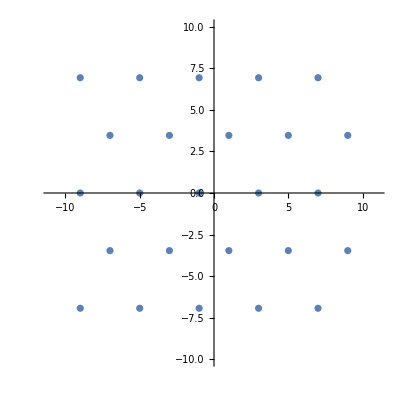

```mathematica
ListPlot[Flatten[pnts⟦2⟧,1],AspectRatio->1, PlotRange-> {{-11,11},{-10,10}},GridLines->{{-10,10},{-10√3/2,10√3/2}}]
```

```mathematica
ClearAll[plotPnts];
 plotPnts[pnts_]:=Module[{Bx=pnts⟦1,5⟧,By=pnts⟦1,6⟧,box},box={{-Bx,Bx},{-By,By}};
 ListPlot[Flatten[pnts⟦2⟧,1],AspectRatio->1,PlotRange->1.1box,GridLines->box]]
```

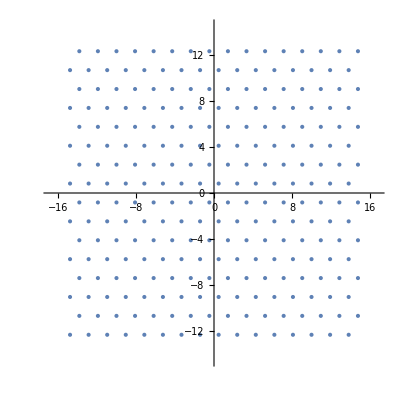

```mathematica
pnts256=fill[Bx[256, 1/π],256];
p256=plotPnts[pnts256]
```

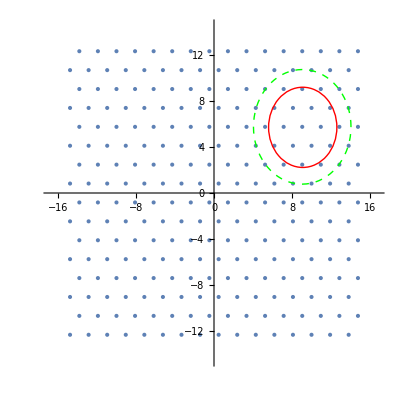

```mathematica
p2=Flatten[pnts256⟦2⟧,1]⟦189⟧;Show[p256,Graphics[ {Red,Circle[p2,3.5]}],
Graphics[{Green, Dashed,Circle[p2, 5]}]]
```

#### Test Data

```mathematica
N[fill[9,9]]
```

{{0.032075,6.,3.,3.,9.,7.79423},{{{-7.5,-5.19615},{-1.5,-5.19615},{4.5,-5.19615}},{{-4.5,0.},{1.5,0.},{7.5,0.}},{{-7.5,5.19615},{-1.5,5.19615},{4.5,5.19615}}}}

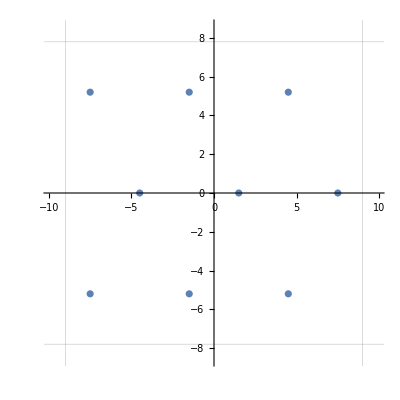

```mathematica
plotPnts[%]
```

#### Potentials 1/r^n

The standard repulsive potential is given by:

```mathematica
ClearAll[rn];
rn[r_, n_]:= 1/r^n
```

Here is the form for a particular n:

```mathematica
rn[r,5]
```

1/r^5

And here are some interesting values of that:

```mathematica
test={1/2, 1, 2,a79, 3, 3.4999, 7/2, 4};
Map[ rn[#,5]&,test]
```

{32,1,1/32,0.0398981,1/243,0.00190424,32/16807,1/1024}

The force is the derivative with respect to r:

```mathematica
f[r_]=D[rn[r,5],r]
```

-5/r^6

Here are the resulting forces at those same interesting values.

```mathematica
Map[f,test]
```

{-320,-5,-5/64,-0.10474,-5/729,-0.00272042,-320/117649,-5/4096}

The skin at 3.5σ yields the following ratios to the mean separation in a hexagonal grid:

```mathematica
{rn[3.5,5]/rn[a79,5],f[3.5]/f[a79]}
```

{0.0477208,0.0259687}

The number of particles expected in a circular region is ρ π r^2, but with the density ρ = 1/π, the expected number of particles is simply r^2

```mathematica
Block[{ρ=1/π},ρ π{3.5^2,5^2}]
```

{12.25,25}

```mathematica
,=
```

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}